# Domača naloga – Mathematica

## 1. naloga

1. Izračunajte vsoto ∑_(k=1)^30 k^2/(k+5).
2. Rešite neenačbo:|x-1|≤ 2x+3 
3. Izračunajte drugi odvod funkcije  3tg (2cos(x)+1)  sin (x) in ga poenostavite.
4. S funkcijo FindRoot numerično izračunajte ničlo funkcije  (cos(x))/(e^(x^3-1)) z začetnim približkom x = 1 .

```mathematica
N[Sum[k^2/(k+5), {k,1, 30}]]
```

361.586

```mathematica
Reduce[Abs[x-1]<=2x+3, x]
```

x≥-2/3

```mathematica
ClearAll
```

ClearAll

```mathematica
f[x_]:=3Tan[2Cos[x]+1]Sin[x]
```

```mathematica
f'[x]
```

-6 Sec[1+2 Cos[x]]^2 Sin[x]^2+3 Cos[x] Tan[1+2 Cos[x]]

```mathematica
Simplify[f'[x]]
```

```mathematica
-6 Sec[1+2 Cos[x]]^2 Sin[x]^2+3 Cos[x] Tan[1+2 Cos[x]]
```

```mathematica
FindRoot[Cos[x]/(x^(x^3-1)),x,1]
```

FindRoot::fdssnv: Search specification x without variables should be a list with 1 to 4 elements.

```mathematica
FindRoot[Cos[x]/(x^(x^3-1)),{x,1}]
```

{x→1.5708}

## 2. naloga

1. Definirajte funkciji x(t)=cos(5t) in y(t)=0.5 sin(t).
2. Poiščite take vrednosti t ∈ [0, π], da velja x(t)=0
3. Narišite parametrično podano krivuljo na območju t ∈[0,2π].

```mathematica
x[t_]:=Cos[5t]
y[t_]:=0.5Sin[t]
```

```mathematica
Reduce[x[t]==0 && 0<=t<=π,t]
```

t==π/10||t==(3 π)/10||t==π/2||t==(7 π)/10||t==(9 π)/10

```mathematica
?ParametricPlot
```

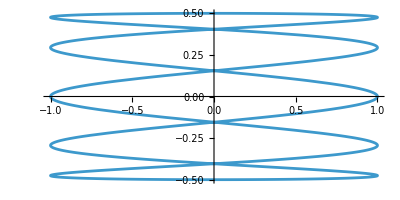

```mathematica
ParametricPlot[{x[t],y[t]},{t,0,2π}]
```